## Experiment 1

```mathematica
xdata={20,40,60,80,99.8};
ydata={2.8,5.4,8.1,10.8,13.5}
```

{2.8,5.4,8.1,10.8,13.5}

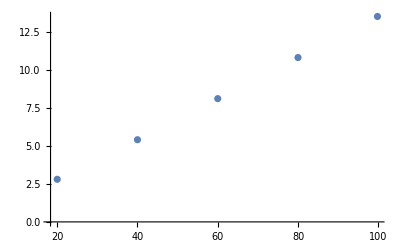

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

```mathematica
data=Transpose[{xdata,ydata}]
```

{{20,2.8},{40,5.4},{60,8.1},{80,10.8},{99.8,13.5}}

```mathematica
expt1fit=LinearModelFit[data,x,x]
```

FittedModel[0.069351+0.134267 x]

```mathematica
expt1fit[10]
```

1.41202

```mathematica
expt1fit[100]
```

13.4961

```mathematica
ex1sumx=Total[xdata]
ex1sumx2=Total[#^2&/@xdata]
ex1sumy=Total[ydata]
ex1sumy2=Total[#^2&/@ydata]
ex1sumxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}]
```

299.8

21960.

40.6

401.5

2969.3

```mathematica
ex1N=Length[xdata]
```

5

```mathematica
ex1Δ=ex1N(ex1sumx2)-(ex1sumx)^2
```

19920.2

```mathematica
ex1a=1/ex1Δ(ex1sumx2*ex1sumy-ex1sumx ex1sumxy)
```

0.069351

```mathematica
ex1b=1/ex1Δ(ex1N ex1sumxy - ex1sumx ex1sumy)
```

0.134267

```mathematica
ex1σ=Sqrt[2]*0.1;
```

```mathematica
ex1da=√((ex1σ^2 ex1sumx2)/ex1Δ)
```

0.148486

```mathematica
ex1db=√((ex1σ^2 ex1N)/ex1Δ)
```

0.00224054

```mathematica
981/(ex1b^2) ex1db
```

121.923

```mathematica
981/ex1b
```

7306.34

## Experiment 2

```mathematica
t1Lst={6.06,7.40,8.25,8.32,9.04}
t2Lst={6.03,7.07,7.59,8.52,9.13}
t3Lst={6.07,6.89,7.75,8.73,8.78}
```

{6.06,7.4,8.25,8.32,9.04}

{6.03,7.07,7.59,8.52,9.13}

{6.07,6.89,7.75,8.73,8.78}

```mathematica
data=Transpose[{t1Lst,t2Lst,t3Lst}];
```

```mathematica
Mean[#]&/@data
(StandardDeviation[#1]/(√3)&)/@data
```

{6.05333,7.12,7.86333,8.52333,8.98333}

{0.0120185,0.149332,0.198774,0.118369,0.104934}

```mathematica
Tlst=(Mean[#]/10)&/@data
```

{0.605333,0.712,0.786333,0.852333,0.898333}

```mathematica
ΔTlst=(StandardDeviation[#1]/(10*√3)&)/@data
```

{0.00120185,0.0149332,0.0198774,0.0118369,0.0104934}

```mathematica
T2Lst=#^2&/@Tlst
```

{0.366428,0.506944,0.61832,0.726472,0.807003}

```mathematica
ΔT=0.016;
```

```mathematica
ΔT2lst=Table[2 Tlst[[i]] ΔT,{i,1,Length[Tlst]}]
```

{0.0193707,0.022784,0.0251627,0.0272747,0.0287467}

```mathematica
ex2ydata=T2Lst
ex2xdata={20,40,60,80,99.8}
```

{0.366428,0.506944,0.61832,0.726472,0.807003}

{20,40,60,80,99.8}

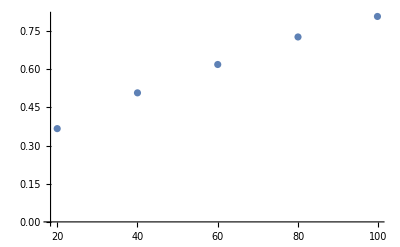

```mathematica
ListPlot[Transpose[{ex2xdata,ex2ydata}]]
```

```mathematica
ex2fit=LinearModelFit[Transpose[{ex2xdata,ex2ydata}],x,x]
```

FittedModel[0.274336+0.0055153 x]

```mathematica
ex2fit[100]
```

0.825866

```mathematica
Solve[ex2fit[x]==0,x]
```

{{x→-49.7409}}

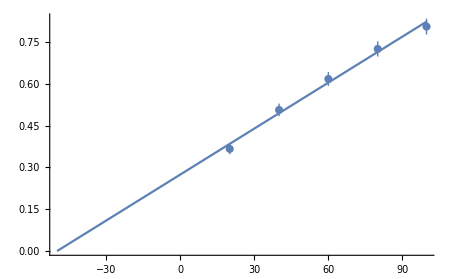

```mathematica
Show[ListPlot[Transpose[{ex2xdata,Table[Around[ex2ydata[[i]],ΔT2lst[[i]]],{i,1,Length[ex2ydata]}]}],AxesOrigin->{-50,0}],Plot[ex2fit[x],{x,-50,100}],AxesOrigin->{0,Automatic}]
```

```mathematica
ex2sumx=Total[ex2xdata]
ex2sumx2=Total[#^2&/@ex2xdata]
ex2sumy=Total[ex2ydata]
ex2sumy2=Total[#^2&/@ex2ydata]
ex2sumxy=Sum[ex2xdata[[i]]ex2ydata[[i]],{i,1,Length[xdata]}]
```

299.8

21960.

3.02517

1.9526

203.362

```mathematica
ex2N=Length[ex2xdata]
```

5

```mathematica
ex1Δ
```

19920.2

```mathematica
ex2Δ=ex2N(ex2sumx2)-(ex2sumx)^2
```

19920.2

```mathematica
ex2a=1/ex2Δ(ex2sumx2*ex2sumy-ex2sumx ex2sumxy)
```

0.274336

```mathematica
ex2b=1/ex2Δ(ex2N ex2sumxy - ex2sumx ex2sumy)
```

0.0055153

```mathematica
LinearModelFit[Transpose[{ex2xdata,ex2ydata}],x,x]
```

FittedModel[0.274336+0.0055153 x]

```mathematica
ex1σ=Sqrt[2]*0.1;
```

```mathematica
981/(ex1b^2) ex1db
```

121.923

```mathematica
981/ex1b
```

7306.34

```mathematica
ex2Δerror=Total[(1/#1^2&)/@ΔT2lst] ∑_(i=1)^Length[ex2xdata] ex2xdata⟦i⟧^2/ΔT2lst⟦i⟧^2-(∑_(i=1)^Length[ex2xdata] ex2xdata⟦i⟧/ΔT2lst⟦i⟧^2)^2
```

6.04335×10^10

```mathematica
ex2da=√((∑_(i=1)^Length[ex2xdata] ex2xdata⟦i⟧^2/ΔT2lst⟦i⟧^2)/ex2Δerror)
```

0.0224615

```mathematica
ex2db=Sqrt[Total[(1/#1^2&)/@ΔT2lst]/ex2Δerror]
```

0.00037997

```mathematica
ex2a/ex2b
```

49.7409

```mathematica
ex2a/ex2b Sqrt[(ex2da/ex2a)^2+(ex2db/ex2b)^2]
```

5.32251

```mathematica
4π^2/ex2b
```

7157.98

```mathematica
4π^2/ex2b^2 * ex2db
```

493.14

```mathematica
variation=Total[(ex2ydata-(ex2a+ex2b#&)/@ex2xdata)^2]/(ex2N-2)
```

0.000360286

```mathematica
Sqrt[variation/(ex2N ex2sumx2-ex2sumx^2) ex2sumx2]
```

0.0199294

```mathematica
ex2da
```

0.0224615

```mathematica
ex2a/ex2b
```

49.7409

```mathematica
Sqrt[(ex2da/ex2a)^2+(ex2db/ex2b)^2]*ex2a/ex2b
```

5.32251

{0.615358,-0.494948,-0.605254,-0.71556,-0.824763}